## Funcs

```mathematica
SetDirectory[ NotebookDirectory[]];
<<"functions/Sensor.mx";
<<"functions/DimRedFunDS.mx";
```

```mathematica
SysProp[fn_]:=Module[{},
samples = 20000;
A = Import["data/"<>fn<>".csv"]/. n_?NumericQ/;n>0->1;
AnN = Dimensions[A]⟦2⟧;
PlN = Dimensions[A]⟦1⟧;An0=ConstantArray[0,{PlN,PlN}];
Pl0 =ConstantArray[0,{AnN,AnN}];
Asq= ArrayFlatten[{{An0,A},{Transpose@A,Pl0}}];
G = DirectedGraph[AdjacencyGraph[Asq],GraphLayout->"BipartiteEmbedding"];
SensorScore = SScalc[G,samples];
or2 = Ordering[SensorScore];
c2=Table[(Blend[{ RGBColor[0.8300000000000001, 0, 1],RGBColor[0, 0.85, 0.65]},Rescale[#,{0,1}]]&)[i],{i,0,1,1/(Length[or2]-1)}];
(*or2 = Ordering[SensorScore];
c2=Table[(Blend[{ RGBColor[0, 0.91, 0.65],RGBColor[0.8300000000000001, 0, 1]},Rescale[#,{0,1}]]&)[i],{i,0,1,1/(Length[or2]-1)}];*)
c2o=Table[c2[[Flatten[Position[or2,i]]]],{i,Length[or2]}];
vs=Table[i-> "Diamond",{i,PlN}];
Gp = UndirectedGraph[AdjacencyGraph[Transpose[Asq]],
	GraphLayout->"RadialEmbedding",
	VertexStyle->Thread[Range[Length[c2o]]->c2o],
	VertexSize->.6,
	EdgeStyle->Opacity[0.5, Gray],
	VertexShapeFunction->vs,
	VertexLabels->Automatic,
	ImageSize->Medium];
CB=BarLegend[{(Blend[{ RGBColor[0.8300000000000001, 0, 1],RGBColor[0, 0.85, 0.65]},Rescale[#,{0,Max@SensorScore}]]&),{0,Max@SensorScore}},
LegendLayout->"Row",
LabelStyle->{FontSize->12}
];
sig =dr[{Max@SensorScore, Skewness@SensorScore}]//First;
fq[s_,r_] := 0.0728597*s^2+−0.000282177*s*r+0.0000353452*r^2+−0.426029;
fr[s_,r_] := −.0262698*s^4+−0.000194251*s*r+−0.00698335*r+0.779287;
r1Pred=ContourPlot[fr[x,y],{x,sig-.00001,sig+.00001},{y, 0, 90},
ImageSize->{Automatic,275},
FrameTicksStyle->11,
Contours->6,
(*Contours->{-0.5,-0.2,-0.171,0.171,0.2,0.5},*)
FrameLabel->{"network structure σ= "<>ToString@sig,"deviations from equilibrium ρ"},
FrameTicks->{{Range[-10,100,20],None},{Range[-10,10,0.5],None}},
(*ColorFunction->(Blend[{RGBColor[0, 0.85, 0.65],White,Gray},Rescale[#,{0,1}]]&),*)
ColorFunction->(Blend[{Gray,White,RGBColor[0, 0.85, 0.65]},#]&),
PlotLegends->Placed[BarLegend[
Automatic, 
LabelStyle->{FontSize->11},
 LegendMarkerSize->260, 
(*Ticks->Range[-2,2,0.5],*)
LegendLayout->"Column"],
 Right],
ColorFunctionScaling->True,
PlotLabel->"r prediction"
(*PlotLegends->Automatic*)
];
qsPred=ContourPlot[fq[x,y],{x,sig-.00001,sig+.00001},{y, 0, 90},
ImageSize->{Automatic,275},
FrameTicksStyle->11,
Contours->6,
(*Contours->{-0.5,-0.2,-0.171,0.171,0.2,0.5},*)
FrameLabel->{"network structure σ_= "<>ToString@sig,"deviations from equilibrium ρ"},
FrameTicks->{{Range[-10,100,20],None},{Range[-10,10,0.5],None}},
(*ColorFunction->(Blend[{RGBColor[0, 0.85, 0.65],White,Gray},Rescale[#,{0,1}]]&),*)
ColorFunction->(Blend[{RGBColor[0, 0.85, 0.65],White,Gray},#]&),
PlotLegends->Placed[BarLegend[
Automatic, 
LabelStyle->{FontSize->11},
 LegendMarkerSize->260, 
(*Ticks->Range[-2,2,0.5],*)
LegendLayout->"Column"],
 Right],
ColorFunctionScaling->True,
PlotLabel-> "q^* prediction"
];
Export["data/data_sensor/"<>fn<>"_SS.csv",SensorScore];
{
{{"Interaction Matrix"},{Graphics[MatrixPlot[A,FrameLabel->{"Plants",None,None,"Animals"},ImageSize->Medium, FrameTicks->{Range[PlN], None, None,Transpose@{Range[AnN],Range[PlN+1,PlN+AnN]}}]]}},
{{"    "},{{"   "}}},
{{"Sensor Score"},
{
{"Plants:",{Range[PlN],Round[SensorScore⟦1;;PlN⟧,.001]}},
{"  "},
{"Animals:",{Range[PlN+1,PlN+AnN],Round[SensorScore⟦PlN+1;;⟧,.001]}}
}
},
{{"    "},{{"   "}}},
{{"Network Properties"},
{
{"Network Size:",AnN+PlN},
{"Number of Plants:",PlN},
{"Number of Animals:",AnN},
{"Number of Specialists:", Length@Position[VertexDegree@Gp,1]},
{"MSS Size:",Length@SensorLin[G]},
{"Max Sensor Score:", Round[Max@SensorScore,.001]},
{"Min Sensor Score:", Round[Min@SensorScore,.001]},
{"Mean Sensor Score:", Round[Mean@SensorScore,.001]},
{"Median Sensor Score:", Round[Median@SensorScore,.001]},
{"Sensor Score Skewness:", Skewness@SensorScore},
{"σ (Network Structure):", sig}
}
},
{{"    "},{{"   "}}},
{{"Network Diagram"},
{{Gp,{"         Sensor Score",CB},{"Plants",Style[" □",Large]},{"Animals",Style[" ○",Large]}}}
},
{{"    "},{{"   "}}},
{{"Ordered List of Species"},
{
{{"By Sensor Score:","(High to Low)"},{Reverse@Ordering[SensorScore+RandomReal[{-.0003,.0003},{Length@SensorScore}]]}},
{"  "},
{{"By Degree:","(Low to High)"},{Ordering[VertexDegree@Gp+RandomReal[{-.0003,.0003},{Length@SensorScore}]]}},
{"  "},
{{"At Random:"," "},{RandomSample@VertexList@Gp}}
}
},
{{"    "},{{"   "}}},
{{"Metrics Predictions"},
{{qsPred, r1Pred}}
}
}//TableForm
]
```

# Main

## Mount Missim

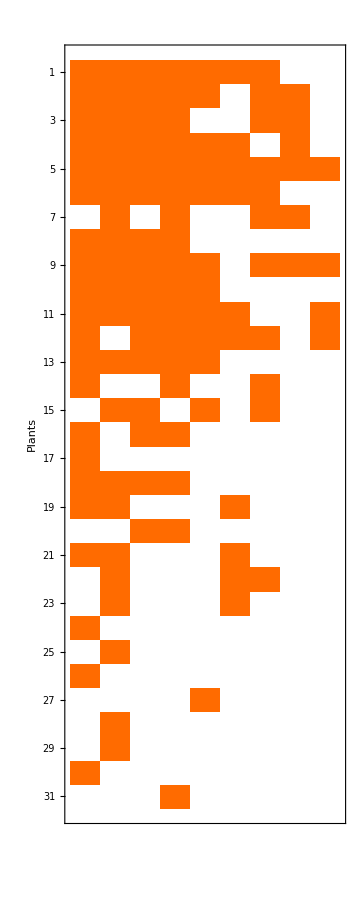
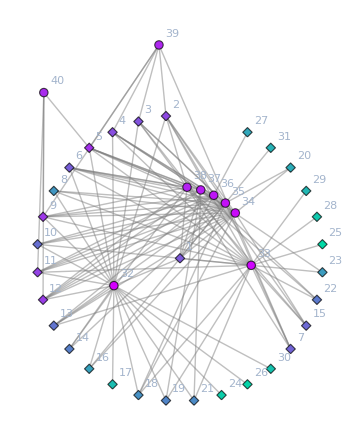
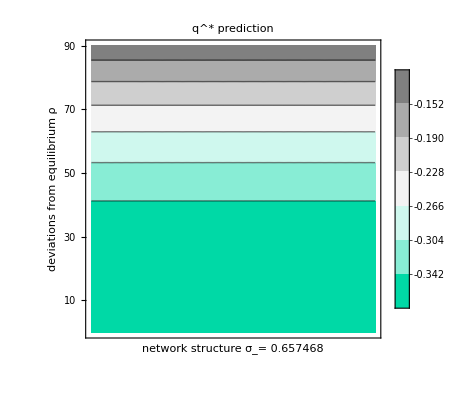
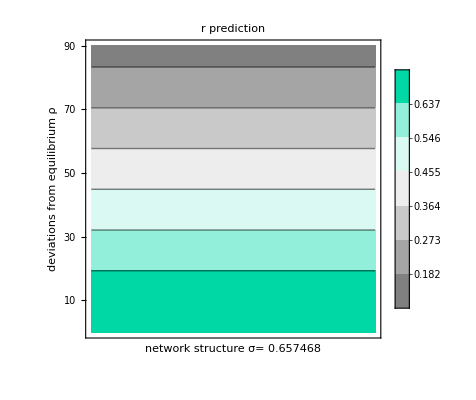
Interaction Matrix | -Graphics-
     |    
Sensor Score | Plants: | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31
0.572 | 0.505 | 0.539 | 0.505 | 0.387 | 0.573 | 0.582 | 0.778 | 0.399 | 0.699 | 0.42 | 0.411 | 0.702 | 0.759 | 0.673 | 0.806 | 0.902 | 0.773 | 0.768 | 0.836 | 0.77 | 0.707 | 0.798 | 0.906 | 0.908 | 0.907 | 0.823 | 0.905 | 0.901 | 0.904 | 0.882
   | 
Animals: | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
     |    
Network Properties | Network Size: | 40
Number of Plants: | 31
Number of Animals: | 9
Number of Specialists: | 9
MSS Size: | 22
Max Sensor Score: | 0.908
Min Sensor Score: | 0.
Mean Sensor Score: | 0.55
Median Sensor Score: | 0.686
Sensor Score Skewness: | -0.694728
σ (Network Structure): | 0.657468
     |    
Network Diagram | -Graphics- |          Sensor Score
 | Plants
 □ | Animals
 ○
     |    
Ordered List of Species | By Sensor Score:
(High to Low) | 25 | 26 | 24 | 28 | 30 | 17 | 29 | 31 | 20 | 27 | 16 | 23 | 8 | 18 | 21 | 19 | 14 | 22 | 13 | 10 | 15 | 7 | 6 | 1 | 3 | 4 | 2 | 11 | 12 | 9 | 5 | 39 | 38 | 34 | 40 | 33 | 35 | 37 | 36 | 32
   | 
By Degree:
(Low to High) | 24 | 26 | 30 | 29 | 25 | 28 | 31 | 17 | 27 | 23 | 20 | 14 | 16 | 22 | 19 | 21 | 8 | 18 | 15 | 40 | 7 | 13 | 10 | 39 | 3 | 2 | 4 | 11 | 6 | 1 | 12 | 9 | 5 | 37 | 38 | 36 | 34 | 35 | 33 | 32
   | 
At Random:
  | 3 | 21 | 4 | 39 | 8 | 7 | 31 | 10 | 40 | 32 | 35 | 2 | 25 | 37 | 17 | 22 | 16 | 18 | 13 | 29 | 19 | 9 | 6 | 36 | 20 | 33 | 38 | 12 | 23 | 30 | 11 | 14 | 26 | 27 | 24 | 34 | 15 | 5 | 1 | 28
     |    
Metrics Predictions | -Graphics- | -Graphics-

```mathematica
fn2 = "M_SD_002"; (*Enter the network matrix csv filename here. The matrix must be rectangular and have plants as rows and animals as columns*)

(*Main function*) 
SysProp[fn2]
```

## Genebra

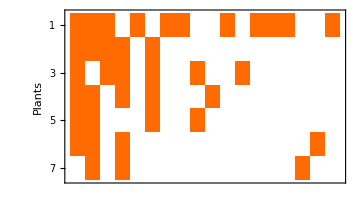
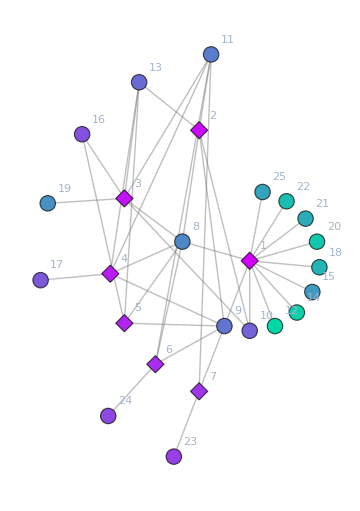
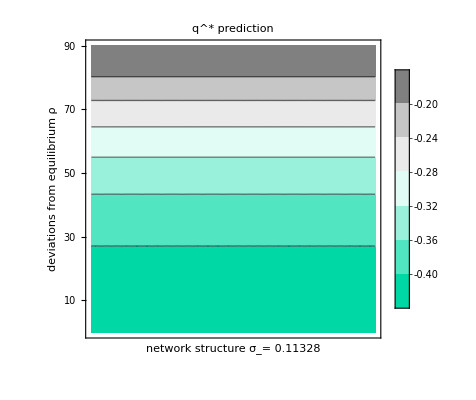
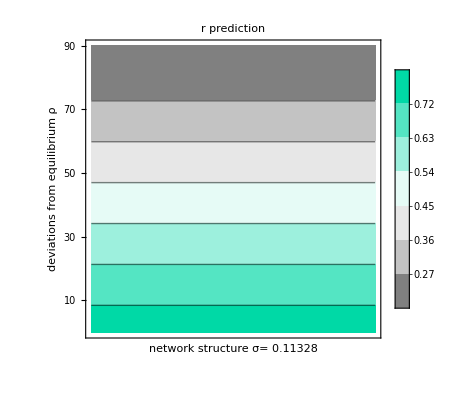
Interaction Matrix | -Graphics-
     |    
Sensor Score | Plants: | 1 | 2 | 3 | 4 | 5 | 6 | 7
0. | 0. | 0. | 0. | 0. | 0. | 0.
   | 
Animals: | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25
0.41 | 0.387 | 0.382 | 0.409 | 0.886 | 0.386 | 0.886 | 0.879 | 0.35 | 0.377 | 0.882 | 0.57 | 0.885 | 0.882 | 0.885 | 0.326 | 0.336 | 0.881
     |    
Network Properties | Network Size: | 25
Number of Plants: | 7
Number of Animals: | 18
Number of Specialists: | 12
MSS Size: | 11
Max Sensor Score: | 0.886
Min Sensor Score: | 0.
Mean Sensor Score: | 0.44
Median Sensor Score: | 0.386
Sensor Score Skewness: | 0.0954913
σ (Network Structure): | 0.11328
     |    
Network Diagram | -Graphics- |          Sensor Score
 | Plants
 □ | Animals
 ○
     |    
Ordered List of Species | By Sensor Score:
(High to Low) | 12 | 14 | 20 | 22 | 18 | 21 | 25 | 15 | 19 | 8 | 11 | 9 | 13 | 10 | 17 | 16 | 24 | 23 | 1 | 5 | 6 | 7 | 4 | 2 | 3
   | 
By Degree:
(Low to High) | 12 | 20 | 19 | 24 | 25 | 21 | 14 | 18 | 17 | 15 | 23 | 22 | 16 | 10 | 7 | 13 | 6 | 5 | 11 | 2 | 4 | 3 | 8 | 9 | 1
   | 
At Random:
  | 25 | 20 | 9 | 8 | 14 | 19 | 5 | 18 | 16 | 17 | 22 | 12 | 15 | 21 | 13 | 2 | 10 | 3 | 24 | 23 | 4 | 7 | 11 | 1 | 6
     |    
Metrics Predictions | -Graphics- | -Graphics-

```mathematica
fn1 = "M_SD_009"; (*Enter the network matrix csv filename here. The matrix must be rectangular and have plants as rows and animals as columns*)

(*Main function*)
SysProp[fn1]
```

## Calton

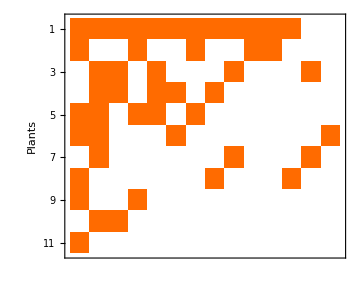
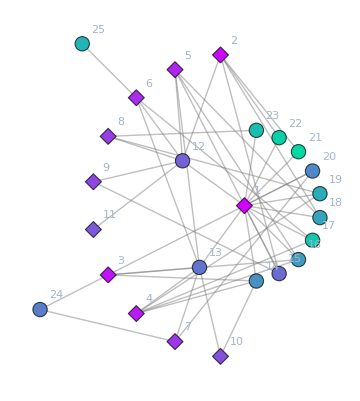
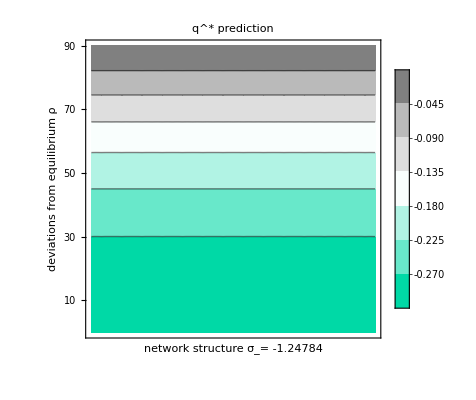
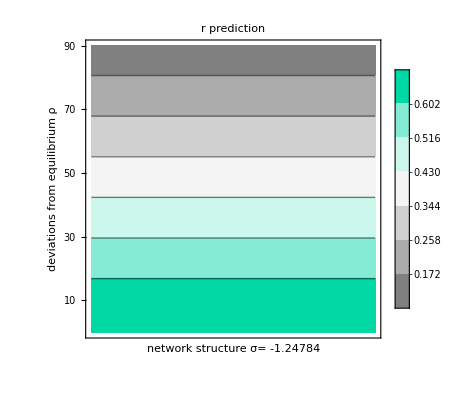
Interaction Matrix | -Graphics-
     |    
Sensor Score | Plants: | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
   | 
Animals: | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25
0. | 0.15 | 0.205 | 0. | 0.214 | 0.297 | 0.224 | 0.252 | 0.188 | 0.396 | 0.384 | 0.259 | 0.178 | 0.254
     |    
Network Properties | Network Size: | 25
Number of Plants: | 11
Number of Animals: | 14
Number of Specialists: | 2
MSS Size: | 3
Max Sensor Score: | 0.396
Min Sensor Score: | 0.
Mean Sensor Score: | 0.12
Median Sensor Score: | 0.
Sensor Score Skewness: | 0.538068
σ (Network Structure): | -1.24784
     |    
Network Diagram | -Graphics- |          Sensor Score
 | Plants
 □ | Animals
 ○
     |    
Ordered List of Species | By Sensor Score:
(High to Low) | 21 | 22 | 17 | 23 | 25 | 19 | 18 | 16 | 14 | 20 | 24 | 13 | 10 | 15 | 4 | 8 | 6 | 3 | 1 | 5 | 9 | 12 | 11 | 2 | 7
   | 
By Degree:
(Low to High) | 25 | 11 | 23 | 24 | 10 | 21 | 9 | 22 | 8 | 20 | 19 | 7 | 17 | 18 | 14 | 6 | 15 | 16 | 3 | 2 | 4 | 5 | 12 | 13 | 1
   | 
At Random:
  | 1 | 4 | 24 | 17 | 9 | 11 | 22 | 21 | 7 | 15 | 14 | 6 | 5 | 20 | 25 | 18 | 13 | 8 | 3 | 19 | 2 | 23 | 12 | 10 | 16
     |    
Metrics Predictions | -Graphics- | -Graphics-

```mathematica
fn3 = "M_SD_011"; (*Enter the network matrix csv filename here. The matrix must be rectangular and have plants as rows and animals as columns*)

(*Main function*)
SysProp[fn3]
```